```mathematica
Quit[];
```

## Runge - Kutta methods

```mathematica
stepperRK1[obtaink_][δt_,BreglistINI_]:=Module[{k1,k2,k3,k4,res},

k1=δt  obtaink[BreglistINI];

res=BreglistINI+k1

]
```

```mathematica
stepperRK2[obtaink_][δt_,BreglistINI_]:=Module[{k1,k2,k3,k4,res},

k1=δt  obtaink[BreglistINI];
k2=δt  obtaink[BreglistINI+1/2 k1];

res=BreglistINI+k2 
]
```

```mathematica
stepperRK4[obtaink_][δt_,BreglistINI_]:=Module[{k1,k2,k3,k4,res},

k1=δt  obtaink[BreglistINI];
k2=δt  obtaink[BreglistINI+1/2 k1];
k3=δt  obtaink[BreglistINI+1/2 k2];
k4=δt obtaink[BreglistINI+k3];

res=BreglistINI+1/6 k1+1/3 k2 +1/3 k3+1/6 k4
]
```

```mathematica
k1=dt g'[t];
k2=dt g'[t+1/2 dt];
k3=dt g'[t+1/2 dt];
k4=dt g'[t+dt];
Series[g[t+dt]-(g[t]+1/6 k1+1/3 k2 +1/3 k3+1/6 k4),{dt,0,5}]
ClearAll[k1,k2,k3,k4]
```

-(g^(5)[t] dt^5)/2880+O[dt]^6

x''[t] = -x[t]

y’[t] = -x[t]

x’[t] = y[t]

```mathematica
{-1}
```

```mathematica
vecDERosc[{y_,x_}]={-x,y}//N;
```

```mathematica
evol[obtaink_][stepper_][tini_,tmax_,δt_][inicond_]:=Module[{reslist,vec,t},

t=tini;

vec=inicond;

reslist={{t,vec⟦2⟧}};

While[t≤tmax,t=t+δt;vec=stepper[obtaink][δt,vec];reslist=Append[reslist,{t,vec⟦2⟧}];];

reslist

]
```

```mathematica
Timing[osctestRK1=evol[vecDERosc][stepperRK1][0,10 2π,1/100][{0,1}];]
```

{0.000026,Null}

```mathematica
Timing[osctestRK2=evol[vecDERosc][stepperRK2][0,10 2π,1/100][{0,1}];]
```

{0.29402,Null}

```mathematica
Timing[osctestRK4=evol[vecDERosc][stepperRK4][0,10 2π,1/100][{0,1}];]
```

{0.000035,Null}

```mathematica
plotharREF=Plot[Cos[t],{t,0,10 2π},PlotStyle->{Magenta,Dashed,Thick}];
```

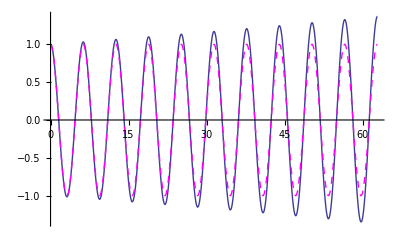

```mathematica
Show[ListPlot[osctestRK1,Joined->True],plotharREF]
```

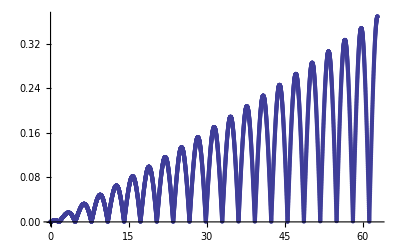

```mathematica
ListPlot[{#⟦1⟧,Abs[#⟦2⟧-Cos[#⟦1⟧]]}&/@osctestRK1]
```

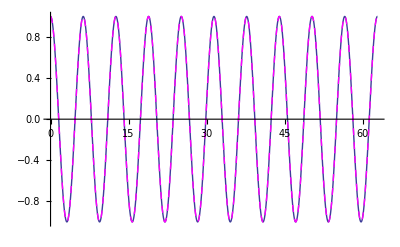

```mathematica
Show[ListPlot[osctestRK2,Joined->True],plotharREF]
```

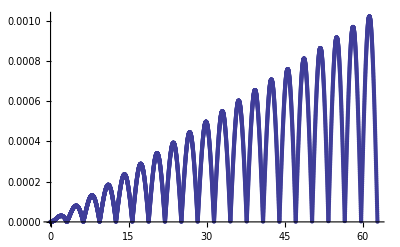

```mathematica
ListPlot[{#⟦1⟧,Abs[#⟦2⟧-Cos[#⟦1⟧]]}&/@osctestRK2]
```

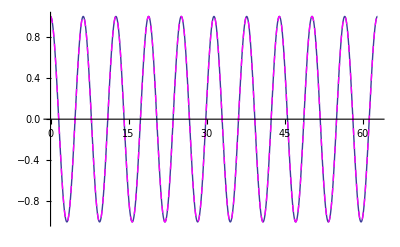

```mathematica
Show[ListPlot[osctestRK4,Joined->True],plotharREF]
```

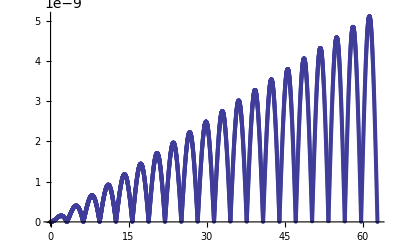

```mathematica
ListPlot[{#⟦1⟧,Abs[#⟦2⟧-Cos[#⟦1⟧]]}&/@osctestRK4]
```

```mathematica
(*use RK4 or similar!*)
```

```mathematica
vecDERoscdamp[{y_,x_}]={-x-2/3 y,y}//N;
```

```mathematica
Timing[oscdamptestRK4=evol[vecDERoscdamp][stepperRK4][0,4π,1/100][{0,1}];]
```

{0.06188,Null}

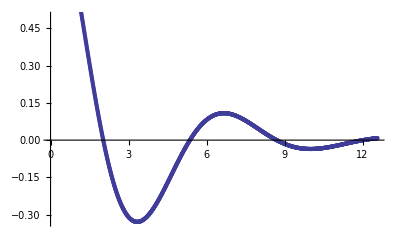

```mathematica
ListPlot[oscdamptestRK4]
```

```mathematica
vecDERoscoverdamp[{y_,x_}]=N[{-x-10y,y}];
```

```mathematica
Timing[oscoverdamptestRK4=evol[vecDERoscoverdamp][stepperRK4][0,30,1/20][{0,1}];]
```

{0.02661,Null}

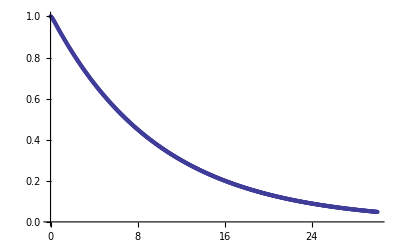

```mathematica
ListPlot[oscoverdamptestRK4]
```

```mathematica
(*below for time dependent setups*)
```

```mathematica
stepperRK4td[obtainktd_][t_,δt_,BreglistINI_]:=Module[{k1,k2,k3,k4,res},

k1=δt  obtainktd[t][BreglistINI];
k2=δt  obtainktd[t+1/2 δt][BreglistINI+1/2 k1];
k3=δt  obtainktd[t+1/2 δt][BreglistINI+1/2 k2];
k4=δt obtainktd[t+δt][BreglistINI+k3];

res=BreglistINI+1/6 k1+1/3 k2 +1/3 k3+1/6 k4
]
```

```mathematica
evoltd[obtainktd_][tini_,tmax_,δt_][inicond_]:=Module[{reslist,vec,t},

t=tini;

vec=inicond;

reslist={{t,vec⟦2⟧}};

While[t≤tmax,vec=stepperRK4td[obtainktd][t,δt,vec];t=t+δt;reslist=Append[reslist,{t,vec⟦2⟧}];];

reslist

]
```

```mathematica
vecDERoscdampforced[t_][{y_,x_}]=N[{-x-1/10 y+5Sin[2/3 t],y}];
```

```mathematica
Timing[oscdampforcedtest=evoltd[vecDERoscdampforced][0,10π,1/100][{0,1}];]
```

{0.21033,Null}

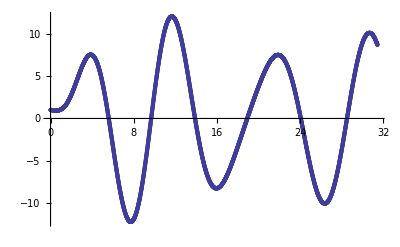

```mathematica
ListPlot[oscdampforcedtest]
```